### Stix "Standard" mode conversion equation (d^4 E)/dx^4+λ^2(x-x_0)(d^2 E)/dx^2+γE=0

#### Dispersion relation for k^2

```mathematica
roots=Solve[k^2+λ^2 x k+γ==0,k]
```

{{k→1/2 (-x λ^2-√(-4 γ+x^2 λ^4))},{k→1/2 (-x λ^2+√(-4 γ+x^2 λ^4))}}

```mathematica
kp=k/.roots[[1]];
km=k/.roots[[2]];
```

```mathematica
rp[x_,λ_,γ_]=kp;
rm[x_,λ_,γ_]=km;
```

### Plot roots γ positive

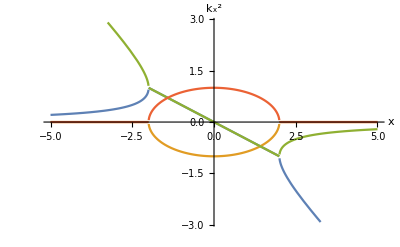

```mathematica
λ=1.;
γ=1.;
Plot[{Re[rp[x,λ,γ]],Im[rp[x,λ,γ]],Re[rm[x,λ,γ]],Im[rm[x,λ,γ]]}, {x,-5,5},AxesLabel->{"x","k_x^2"}]
```

### Plot roots γ negative

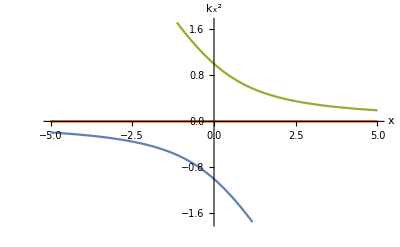

```mathematica
λ=1.;
γ=-1.;
Plot[{Re[rp[x,λ,γ]],Im[rp[x,λ,γ]],Re[rm[x,λ,γ]],Im[rm[x,λ,γ]]}, {x,-5,5},AxesLabel->{"x","k_x^2"}]
```